# L2 Shape function and Derivates

## Isoparametric Formulation of Shape functions:

```mathematica
Quit[];
```

### L2 element

Based on linear polynomial, u^e(x_) = α_0^e+α_1^e x

```mathematica
coef = ({{Subscript[α, 0]}, {Subscript[α, 1]}});
p[x_]:= ({{1, x}})
M= ({{1, Subscript[x, 1]}, {1, Subscript[x, 2]}});
```

```mathematica
u=  p[x].coef
```

(α_0+x α_1)

```mathematica
Ne[x_]:= p[x].Inverse[M]
```

```mathematica
Ne[x] //Simplify
```

((x-x_2)/(x_1-x_2) | (x_1-x)/(x_1-x_2))

### Test L2 element

```mathematica
Ne[Subscript[x, 1]] // Simplify
Ne[Subscript[x, 2]] // Simplify
```

(1 | 0)

(0 | 1)

```mathematica
Sum[Ne[x][[1,i]],{i,1,2}] //Simplify
```

1

### L2 Isoparametric Formulation

```mathematica
(* set Subscript[x, 2]-Subscript[x, 1] = l^e, and choose l^e= 2ξ, such that ξ= -1  and ξ= 1 *)
(* ξ = (Subscript[x, 2]+Subscript[x, 1])/2+ (Subscript[x, 2]-Subscript[x, 1])/2 x -> ξ = (Subscript[x, 2]+Subscript[x, 1])/2+ ξ x -> *)
```

```mathematica
x-Subscript[x, 2]= ξ-1
x-Subscript[x, 1]= ξ+1
```

```mathematica
Ne[x]  /.Subscript[x, 2]-> 1-ξ+x/.Subscript[x, 1]-> -ξ-1+x//Simplify
```

((1-ξ)/2 | (ξ+1)/2)

```mathematica
NL2[ξ_]:=  ({{(1-ξ)/2, (ξ+1)/2}})
```

### Test L2 Isoparametric Formulation

```mathematica
NL2[-1]
NL2[1]
```

(1 | 0)

(0 | 1)

```mathematica
Sum[NL2[ξ][[1,i]],{i,1,2}] //Simplify
```

1

### Plot isoparametric shape functions

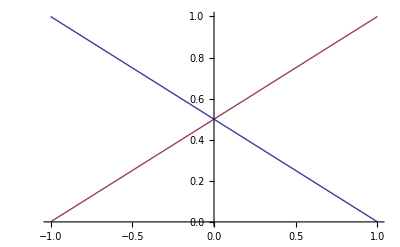

```mathematica
Plot[Tooltip[{NL2[ξ][[1,1]],NL2[ξ][[1,2]]}],{ξ,-1,1}]
```